## Figure 8 of

# “Agent-Based Modeling in Economics and Finance: Past, Present, and Future”

## by Robert Axtell and Doyne Farmer

## Forthcoming in the Journal of Economic Literature

## Background

We queried Google Scholar for the number of papers that explicitly mention “game theory”, “behavioral economics”, “experimental economics”, “individual-based model”, “multi-agent system”, or “agent-based model”. The papers were partitioned into 5 year bins, based on when they appeared. Time series plots were created and the data compared. The exact way this was done is descrirbed in detail below. Figure 8 in the paper is the culmination of several distinct plots.

## 1. Game theory data

First the relevant years for the game theory papers:

```mathematica
gtTime={1940,1945,1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015};
```

Next, here are the data obtained by querying Google Scholar on November 24, 2016. These are counts of papers appearing in the time ‘buckets’ above:

```mathematica
gameTheoryData={5,4,10,65,185,354,590,820,964,1286,2040,3040,4120,7780,14140,17280};
```

Of course, once ‘game theory’ becamse common it may be that some authors did not feel the need to use the term. Put the data in a form suitable for the ListPlot[] routine:

```mathematica
gtData=Table[{gtTime[[i]],gameTheoryData[[i]]},{i,Length[gtTime]}];
```

Do the plot next:

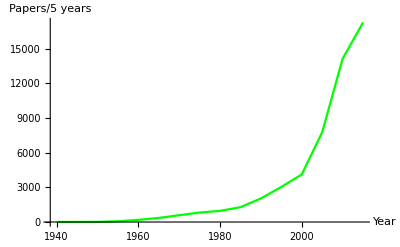

```mathematica
p1=ListPlot[gtData,Joined->True,PlotStyle->Green,AxesLabel->{"Year","Papers/5 years"}]
```

Next the plot with the ordinate logged:

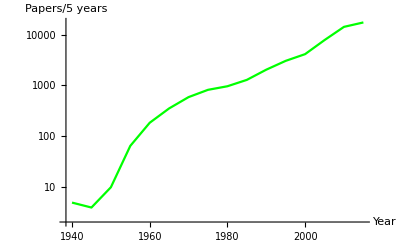

```mathematica
p1L=ListLogPlot[gtData,Joined->True,PlotStyle->Green,AxesLabel->{"Year","Papers/5 years"}]
```

## Behavioral and experimental economics data

### Behavioral economics data

```mathematica
behavioralData={8,16,24,34,182,271,370,787,941,1660,5070,14000,17300};
```

```mathematica
bData=Table[{gtTime[[i+3]],behavioralData[[i]]},{i,Length[gtTime]-3}]
```

{{1955,8},{1960,16},{1965,24},{1970,34},{1975,182},{1980,271},{1985,370},{1990,787},{1995,941},{2000,1660},{2005,5070},{2010,14000},{2015,17300}}

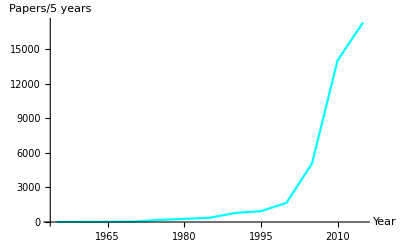

```mathematica
p2=ListPlot[bData,Joined->True,PlotStyle->Cyan,AxesLabel->{"Year","Papers/5 years"}]
```

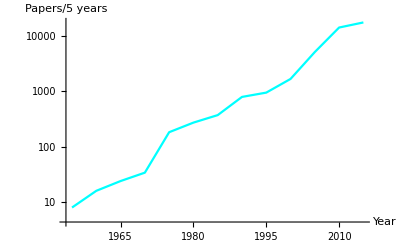

```mathematica
p2L=ListLogPlot[bData,Joined->True,PlotStyle->Cyan,AxesLabel->{"Year","Papers/5 years"}]
```

### Experimental economics data

```mathematica
experimentalData={4,6,4,32,65,155,308,638,2300,2560,6930,13200,16200};
```

```mathematica
eData=Table[{gtTime[[i+3]],experimentalData[[i]]},{i,Length[gtTime]-3}];
```

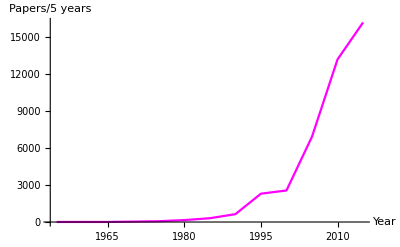

```mathematica
p3=ListPlot[eData,Joined->True,PlotStyle->Magenta,AxesLabel->{"Year","Papers/5 years"}]
```

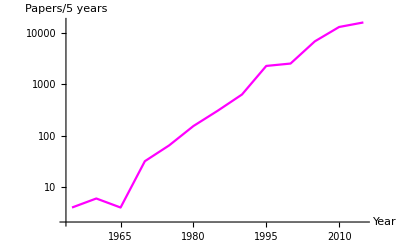

```mathematica
p3L=ListLogPlot[eData,Joined->True,PlotStyle->Magenta,AxesLabel->{"Year","Papers/5 years"}]
```

## Agent data

Let’s use annual time for these data:

```mathematica
aTime = Table[i+1985,{i,30}];
```

### Individual-based models (IBMs), primarily in ecology and evolutionary biology

```mathematica
IBMdata={0,8,13,22,22,30,44,60,69,79,126,197,212,216,280,310,379,475,487,533,653,667,781,910,947,1030,1060,1170,1200,1220};
```

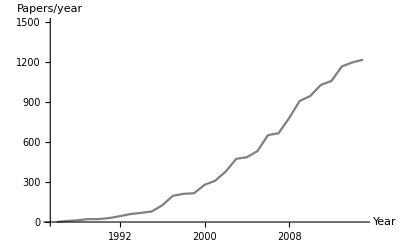

```mathematica
p4=ListPlot[Table[{aTime[[i]],IBMdata[[i]]},{i,Length[aTime]}],Joined->True,PlotStyle->Gray,AxesLabel->{"Year","Papers/year"},PlotRange->{0,1500}]
```

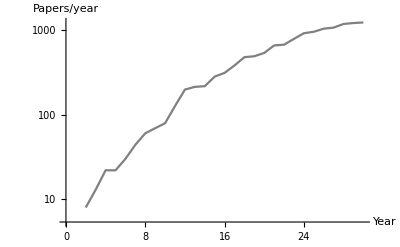

```mathematica
p4L=ListLogPlot[IBMdata,Joined->True,PlotStyle->Gray,AxesLabel->{"Year","Papers/year"}]
```

### Multi-agent systems (MAS), primarily in CS/AI

```mathematica
MASdata={17,13,17,34,52,88,149,212,357,501,773,1010,1560,1980,2620,3350,4190,5360,6570,7800,8400,9240,9580,10900,10800,11100,11600,12600,12500,12500};
```

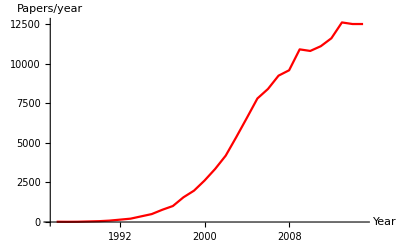

```mathematica
p5=ListPlot[Table[{aTime[[i]],MASdata[[i]]},{i,Length[aTime]}],Joined->True,PlotStyle->Red,AxesLabel->{"Year","Papers/year"}]
```

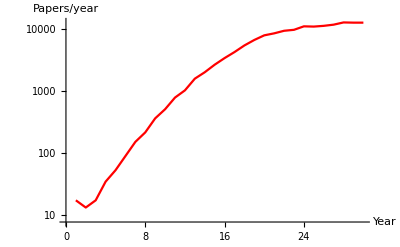

```mathematica
p5L=ListLogPlot[MASdata,Joined->True,PlotStyle->Red,AxesLabel->{"Year","Papers/year"}]
```

### Agent-based models (ABMs), primarily in the social sciences

```mathematica
ABMdata={0,3,6,6,1,10,13,15,27,22,30,43,75,105,201,281,386,535,789,958,1210,1470,1750,2090,2400,2730,3230,3630,3850,4190};
```

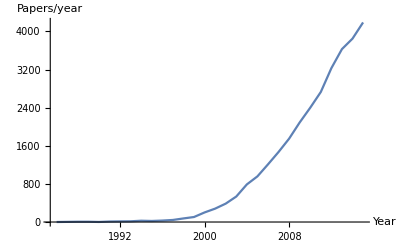

```mathematica
p6=ListPlot[Table[{aTime[[i]],ABMdata[[i]]},{i,Length[aTime]}],Joined->True,AxesLabel->{"Year","Papers/year"}]
```

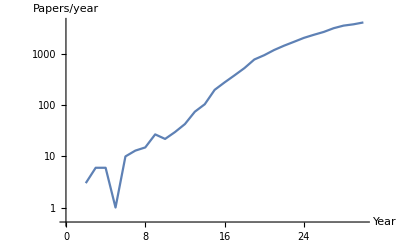

```mathematica
p6L=ListLogPlot[ABMdata,Joined->True,AxesLabel->{"Year","Papers/year"}]
```

#### ABMs over 5 year blocks

```mathematica
FiveYrData=Table[{aTime[[i+4]],Sum[ABMdata[[j]],{j,i,i+4}]},{i,1,Length[aTime],5}]
```

{{1990,16},{1995,87},{2000,454},{2005,2949},{2010,8920},{2015,17630}}

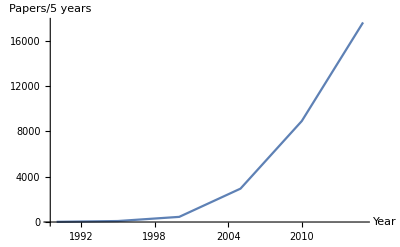

```mathematica
p6FiveYr=ListPlot[FiveYrData,Joined->True,AxesLabel->{"Year","Papers/5 years"}]
```

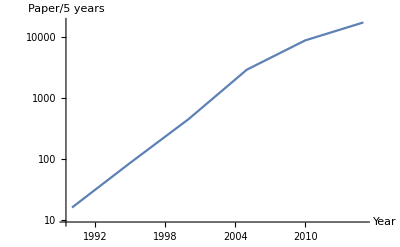

```mathematica
p6FiveYrL=ListLogPlot[FiveYrData,Joined->True,AxesLabel->{"Year","Paper/5 years"}]
```

### Comparison of agent data

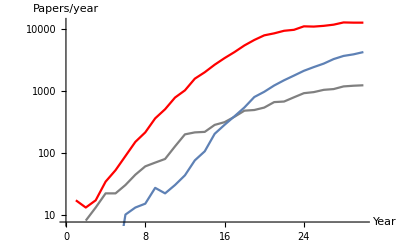

```mathematica
Show[p5L,p4L,p6L]
```

## Comparison

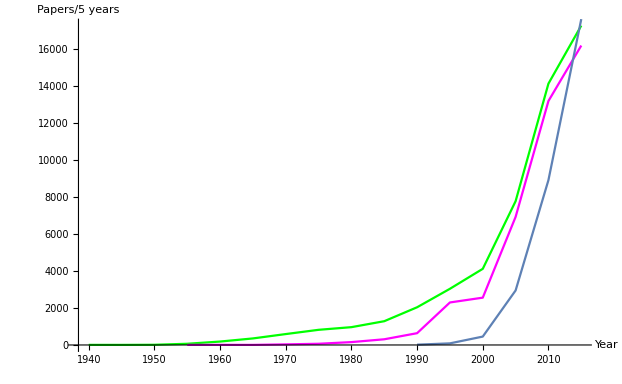

```mathematica
Show[p1,p3,p6FiveYr]
```

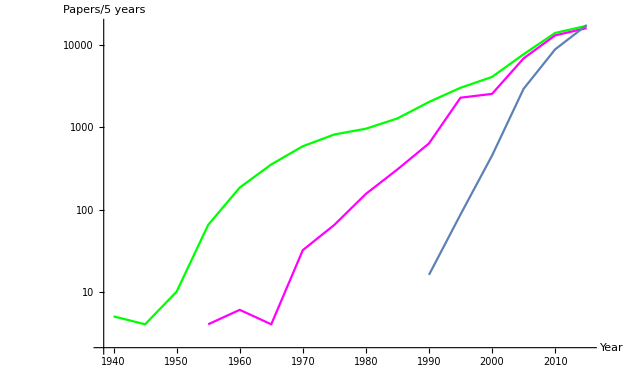

```mathematica
Show[p1L,p3L,p6FiveYrL]
```